## Write Data to files.

Preparing

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica

Test Legend fuctioning.

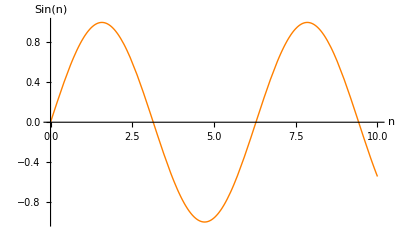

```mathematica
(*********************************************)
Print[Style["Preparing",30,Bold,Orange]]
(*********************************************)
Needs["PlotLegends`"]
SetDirectory["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\"]
(*********************************************)
(*Manually set the start point(a<1) of this table.*)
tranzs=37 ;tranzDE1=29;tranzDE2=29;tranzL=28;
(*Manually set the criteria for the element in aokTabL etc that corresponds to normalization time.*)
norts=138-tranzs;nortL=138-tranzL;nort1=138-tranzDE1;nort2=138-tranzDE2;
(*k1,k2 should not equal to kDE1 at first. Should keep this when calculating!!!!*)
(**************************)
Print[Style["Test Legend fuctioning.",30,Bold,Orange]]
Plot[Sin[n],{n,0,10},PlotStyle->Orange,AxesLabel-> {"n","Sin(n)"},PlotLegend->{"Sin"},LegendPosition->{1.1,-0.4}]
```

```mathematica
(*********************************************)
Print[Style["Parameters",30,Bold,Orange]]
(*********************************************)
wL=-1;
w1 =-0.9;
w2=-0.9;
δ2=-0.000001;
ΩDE0 =0.73;
Ωk0=0;
Ωm0 =0.27;
Ωr0 =8.09*10^-5;
h=0.71;
ce21=0.012;
ce22=0.012;
(*h=1;*)
 (*H0 =(100 h)/300000;*)
H0=100 h;(*the real value is not very important here. this means all length units are MPc/h, all wavenumber units are h/MPc*)
Ωm0s =1; 
Ωr0s =8.09*10^-5;
(*Ωr0s=0;*)
nzs=nzL=nz2=nz3=nz4=aeq=Ωr0/Ωm0
c=300000
```

Parameters

0.00029963

300000

```mathematica
(*********************************************)
Print[Style["Intial conditions for Hubble constant, normalized at early time",30,Bold,Orange]]
(*********************************************)
HL0=H10=H20=H0;
Hs0=H0;
```

Intial conditions for Hubble constant, normalized at early time

```mathematica
(*********************************************)
Print[Style["Define Hubble functions",30,Bold,Orange]]
(*********************************************)
Hs[a_]:= Hs0  √(Ωr0s a^-4+Ωm0s a^-3);mHs[a_]=a Hs[a];
HL[a_]:= HL0  √(Ωr0 a^-4+Ωm0 a^-3+ ΩDE0);mHL[a_]=a HL[a];
H1[a_]:= H10 √(Ωr0 a^-4+Ωm0 a^-3+1/(δ2+w1)ΩDE0 a^-3(δ2+w1 a^(-3(δ2+w1))));mH1[a_]=a H1[a];
H2[a_]:= H20 √(Ωr0 a^-4+Ωm0 a^-3+ 1/(δ2+w2)ΩDE0 a^-3(δ2+w2 a^(-3(δ2+w2))));mH2[a_]=a H2[a];
iHs[a_]:= Hs0  √(Ωm0s a^-1);
iHL[a_]:= HL0  √(Ωm0 a^-1+1/(δ2+wL)ΩDE0 a^-3(δ2+wL a^(-3(δ2+wL))))
iH1[a_]:= H10 √(Ωm0 a^-1+ 1/(δ2+w1)ΩDE0 a^-1(δ2+w1 a^(-3(δ2+w1))))
iH2[a_]:= H20 √(Ωm0 a^-1+  1/(δ2+w2)ΩDE0 a^-1(δ2+w2 a^(-3(δ2+w2))))
```

Define Hubble functions

```mathematica
(*********************************************)
Print[Style["Particle Horizon",30,Bold,Orange]]
(*********************************************)
dHs[a_?NumberQ]:=c a NIntegrate[1/(Hs[x] x^2),{x,0,a}];
dHL[a_?NumberQ]:=c a NIntegrate[1/(HL[x] x^2),{x,0,a}];
dH1[a_?NumberQ]:=c a NIntegrate[1/(H1[x] x^2),{x,0,a}];
dH2[a_?NumberQ]:=c a NIntegrate[1/(H2[x] x^2),{x,0,a}];
```

Particle Horizon

```mathematica
(*********************************************)
Print[Style["Define k of a",30,Bold,Orange]]
(*********************************************)
kL[a_]:= 1/dHL[a];ks[a_]:= 1/dHs[a];kDE1[a_]:= 1/dH1[a];kDE2[a_]:=1/dH2[a];
1/dHL[0.01]
{keqL=1/dHL[aeq],keq1=1/dH1[aeq],keq2=1/dH2[aeq]}
{k0L=1/dHL[1],k01=1/dH1[1],k02=1/dH2[1]}
(*ss[k_]:=NSolve[k==Subscript[H, 1][Subscript[a, 1]]&&Subscript[a, 1]>0,Subscript[a, 1]]//FullSimplify
Solve[k== H2[a2],a2];*)
```

Define k of a

0.0730456

{28.6212,28.6212,28.6212}

{0.0000699507,0.0000706928,0.0000706928}

```mathematica
(*********************************************)
Print[Style["Define growth factors",30,Bold,Orange]]
(*********************************************)
(*
I am not sure what initial conditions to impose. So I just tried the adiabatic initial condition that says Subscript[δ, de]=1/4 Subscript[δ, γ], Subscript[θ, de]=Subscript[θ, γ]
*)
λ1[a_]=(ΩDE0  a^(-3(δ2 +w1)))/(Ωm0+δ2/(δ2+w1)ΩDE0(1-a^(-3(δ2+w1))));
λ2[a_]=(ΩDE0  a^(-3(δ2 +w2)))/(Ωm0+δ2/(δ2+w2)ΩDE0(1-a^(-3(δ2+w2))));
Growths[a_]:= 5/2 Ωm0s  Hs[a]/Hs0 NIntegrate[1/(iHs[x]/Hs0)^3,{x,0,a}];
GrowthL[a_]:= 5/2 Ωm0  HL[a]/HL0 NIntegrate[1/(iHL[x]/HL0)^3,{x,0,a}];
```

Define growth factors

Import power spectrum of LCDM calculated by cmbeasy, and some test

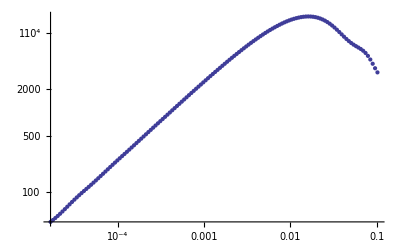

0.0000167287

0.000165215

410.33

138

0.0000118774==71. √(0.73+0.0000809/aL^4+0.27/aL^3)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{aL→-0.717717},{aL→-0.00029963}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{aL→-0.717717},{aL→-0.00029963}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a1→5.26945×10^44}}

{a1→4.63591}

```mathematica
(*********************************************)
Print[Style["Import power spectrum of LCDM calculated by cmbeasy, and some test",30,Bold,Orange]]
(*********************************************)
PowerS=Import["cdm_11-27_cut.dat"];
ListLogLogPlot[PowerS]
(*The k in PowerS is in unit of h MPc^-1. Be careful when calculating.*)
PowerS[[1,1]]
PowerS[[tranzs]][[1]]
PowerS[[tranzs]][[2]]
leth=Length[PowerS]
PowerS[[1,1]]h== HL[aL]
Solve[PowerS[[1,1]]h== HL[aL],aL,Reals]
NSolve[PowerS[[1,1]]h== HL[aL],aL,Reals]
NSolve[PowerS[[1,1]]h==H1[a1],a1,Reals]
FindRoot[PowerS[[1,1]]h==kDE1[a1],{a1,0.0001}]
```

```mathematica
(*********************************************)
Print[Style["Tests for Hubble equations",30,Bold,Orange]]
(*********************************************)
HL[1]/h
HL[0.01]/h
HL[0.001]/h
HL[0.0001]/h
HL[0.00001]/h
HL[0.000001]/h
```

Tests for Hubble equations

100.004

52734.3

1.87323×10^6

1.03875×10^8

9.1433×10^9

9.00944×10^11

```mathematica
(*Once done, can be imported easily.*)
```

```mathematica
aokTabs11=Table[as/.FindRoot[PowerS[[i,1]]h==ks[as],{as,0.0001}],{i,1,leth}];
Export["DEInteracting\\2012-02-21\\aokTabs11.xls",aokTabs11,"XLS"]
aokTabL11=Table[aL/.FindRoot[PowerS[[i,1]]h==kL[aL],{aL,0.0001}],{i,1,leth}];
Export["DEInteracting\\2012-02-21\\aokTabL11.xls",aokTabL11,"XLS"]
aokTabDE111=Table[a1/.FindRoot[PowerS[[i,1]]h==kDE1[a1],{a1,0.0001}],{i,1,leth}];
Export["DEInteracting\\2012-02-21\\aokTabDE111.xls",aokTabDE111,"XLS"]
aokTabDE211=Table[a2/.FindRoot[PowerS[[i,1]]h==kDE2[a2],{a2,0.0001}],{i,1,leth}];
Export["DEInteracting\\2012-02-21\\aokTabDE211.xls",aokTabDE211,"XLS"]
```

DEInteracting\2012-02-21\aokTabs11.xls

DEInteracting\2012-02-21\aokTabL11.xls

DEInteracting\2012-02-21\aokTabDE111.xls

DEInteracting\2012-02-21\aokTabDE211.xls

```mathematica
(*********************************************)
Print[Style["Create tables for power spectrums, and test",30,Bold,Orange]]
(*********************************************)
(*Manually set the start point(a≤1) of this table.*)(*Moved to the beginning of the file.*)
(*tranzs=43;tranzL=43;tranzDE2=43;tranzDE3=43;tranzDE4=43;*)
(********)
aokTabs=Table[as/.FindRoot[PowerS[[i,1]]h==ks[as],{as,0.0001}],{i,tranzs+1,leth}];
Export["DEInteracting\\2012-02-21\\aokTabs.xls",aokTabs,"XLS"]
aokTabL=Table[aL/.FindRoot[PowerS[[i,1]]h==kL[aL],{aL,0.0001}],{i,tranzL+1,leth}];
Export["DEInteracting\\2012-02-21\\aokTabL.xls",aokTabL,"XLS"]
aokTabDE1=Table[a1/.FindRoot[PowerS[[i,1]]h==kDE1[a1],{a1,0.0001}],{i,tranzDE1+1,leth}];
Export["DEInteracting\\2012-02-21\\aokTabDE1.xls",aokTabDE1,"XLS"]
aokTabDE2=Table[a2/.FindRoot[PowerS[[i,1]]h==kDE2[a2],{a2,0.0001}],{i,tranzDE2+1,leth}];
Export["DEInteracting\\2012-02-21\\aokTabDE2.xls",aokTabDE2,"XLS"]
(*Check the results*)
aokTabs[[1]]
Length[aokTabL]
Length[aokTabs]
Length[aokTabDE1]
Length[aokTabDE2]
aokTabs
aokTabL
aokTabDE1
aokTabDE2
```

Create tables for power spectrums, and test

DEInteracting\2012-02-21\aokTabs.xls

DEInteracting\2012-02-21\aokTabL.xls

DEInteracting\2012-02-21\aokTabDE1.xls

DEInteracting\2012-02-21\aokTabDE2.xls

0.969971

110

101

109

109

{0.969971,0.929815,0.891325,0.854431,0.819066,0.785167,0.752673,0.721527,0.691671,0.663053,0.635621,0.609326,0.584121,0.55996,0.536801,0.514601,0.493321,0.472923,0.453371,0.434628,0.416662,0.39944,0.382931,0.367107,0.351938,0.337397,0.323458,0.310097,0.297289,0.285012,0.273243,0.261961,0.251146,0.240779,0.230841,0.221315,0.212183,0.203429,0.195037,0.186992,0.179281,0.171888,0.164802,0.158008,0.151496,0.145253,0.139268,0.133531,0.128031,0.122758,0.117704,0.112858,0.108213,0.10376,0.0994909,0.0953982,0.0914747,0.0877133,0.0841073,0.0806502,0.077336,0.0741586,0.0711125,0.0681922,0.0653924,0.0627082,0.0601349,0.0576677,0.0553024,0.0530347,0.0508605,0.048776,0.0467775,0.0448614,0.0430243,0.041263,0.0395743,0.0379551,0.0364027,0.0349143,0.0334872,0.0321189,0.0308069,0.0295489,0.0283427,0.0271862,0.0260773,0.025014,0.0239944,0.0230168,0.0220793,0.0211804,0.0203185,0.019492,0.0186994,0.0179394,0.0172106,0.0165117,0.0158416,0.0151989,0.0145826}

{0.993808,0.946477,0.901829,0.859686,0.819877,0.782247,0.746649,0.712948,0.681017,0.65074,0.622009,0.594724,0.568793,0.544132,0.520663,0.498313,0.477017,0.456712,0.437343,0.418857,0.401206,0.384346,0.368235,0.352834,0.338107,0.324022,0.310546,0.29765,0.285307,0.27349,0.262176,0.251342,0.240965,0.231025,0.221504,0.212381,0.203641,0.195265,0.187239,0.179548,0.172176,0.165111,0.158339,0.151848,0.145626,0.139661,0.133944,0.128462,0.123208,0.11817,0.113341,0.10871,0.104271,0.100015,0.0959338,0.092021,0.0882695,0.0846723,0.0812232,0.0779161,0.0747449,0.0717042,0.0687884,0.0659925,0.0633114,0.0607405,0.0582751,0.0559109,0.0536438,0.0514696,0.0493846,0.0473851,0.0454676,0.0436287,0.041865,0.0401736,0.0385515,0.0369957,0.0355036,0.0340725,0.0327,0.0313835,0.0301208,0.0289097,0.0277481,0.0266339,0.0255651,0.0245399,0.0235566,0.0226133,0.0217084,0.0208404,0.0200077,0.0192089,0.0184426,0.0177074,0.0170022,0.0163255,0.0156764,0.0150536,0.014456,0.0138827,0.0133326,0.0128048,0.0122983,0.0118123,0.011346,0.0108986,0.0104692,0.0100571}

{0.954222,0.909173,0.866609,0.826369,0.788303,0.752272,0.718145,0.685799,0.655122,0.62601,0.598363,0.572092,0.547113,0.523348,0.500725,0.479178,0.458644,0.439065,0.42039,0.402568,0.385553,0.369303,0.353777,0.33894,0.324755,0.311191,0.298217,0.285805,0.273927,0.262559,0.251677,0.241258,0.231282,0.221727,0.212577,0.203811,0.195414,0.187369,0.17966,0.172274,0.165196,0.158413,0.151912,0.145682,0.13971,0.133986,0.128499,0.12324,0.118198,0.113365,0.108731,0.104289,0.10003,0.0959474,0.0920329,0.0882797,0.0846812,0.081231,0.0779227,0.0747507,0.0717092,0.0687928,0.0659963,0.0633147,0.0607433,0.0582776,0.0559131,0.0536456,0.0514712,0.049386,0.0473864,0.0454687,0.0436296,0.0418658,0.0401743,0.0385521,0.0369962,0.0355041,0.0340729,0.0327003,0.0313838,0.0301211,0.02891,0.0277483,0.026634,0.0255653,0.0245401,0.0235567,0.0226134,0.0217085,0.0208405,0.0200078,0.019209,0.0184427,0.0177075,0.0170022,0.0163256,0.0156764,0.0150536,0.014456,0.0138827,0.0133326,0.0128048,0.0122983,0.0118124,0.011346,0.0108986,0.0104692,0.0100571}

{0.954222,0.909173,0.866609,0.826369,0.788303,0.752272,0.718145,0.685799,0.655122,0.62601,0.598363,0.572092,0.547113,0.523348,0.500725,0.479178,0.458644,0.439065,0.42039,0.402568,0.385553,0.369303,0.353777,0.33894,0.324755,0.311191,0.298217,0.285805,0.273927,0.262559,0.251677,0.241258,0.231282,0.221727,0.212577,0.203811,0.195414,0.187369,0.17966,0.172274,0.165196,0.158413,0.151912,0.145682,0.13971,0.133986,0.128499,0.12324,0.118198,0.113365,0.108731,0.104289,0.10003,0.0959474,0.0920329,0.0882797,0.0846812,0.081231,0.0779227,0.0747507,0.0717092,0.0687928,0.0659963,0.0633147,0.0607433,0.0582776,0.0559131,0.0536456,0.0514712,0.049386,0.0473864,0.0454687,0.0436296,0.0418658,0.0401743,0.0385521,0.0369962,0.0355041,0.0340729,0.0327003,0.0313838,0.0301211,0.02891,0.0277483,0.026634,0.0255653,0.0245401,0.0235567,0.0226134,0.0217085,0.0208405,0.0200078,0.019209,0.0184427,0.0177075,0.0170022,0.0163256,0.0156764,0.0150536,0.014456,0.0138827,0.0133326,0.0128048,0.0122983,0.0118124,0.011346,0.0108986,0.0104692,0.0100571}

Plot k of a

0.000119402

0.0000699507

0.0000706928

28.5557

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.0000862641}. NIntegrate obtained -0.00024017 + 0.00912658\ ⅈ and 0.0000301288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.000327511}. NIntegrate obtained -0.000898138 + 0.0175416\ ⅈ and 0.0000957909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.000327511}. NIntegrate obtained -0.000905131 - 0.0175426\ ⅈ and 0.0000957876 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

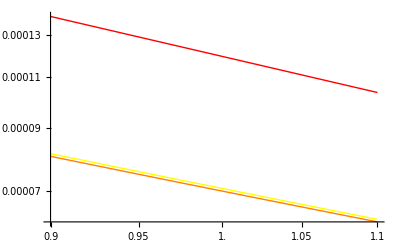

```mathematica
(*********************************************)
Print[Style["Plot k of a",30,Bold,Orange]]
(*********************************************)
ks[1]
kL[1]
kDE1[1]
kL[3*10^-4]
LogLogPlot[{ks[a],kL[a],kDE2[a]},{a,0.9,1.1},PlotStyle->{Red,Orange,Yellow}]
```

```mathematica
(*Finished dealing with k~a relations.*)
```

```mathematica
(*
aokTabs111=Import["DEInteracting\\2012-02-21\\aokTabs11.xls"];
aokTabs11=Table[aokTabs111[[1]][[i]][[1]],{i,1,leth}]
aokTabL111=Import["DEInteracting\\2012-02-21\\aokTabL11.xls"];
aokTabL11=Table[aokTabL111[[1]][[i]][[1]],{i,1,leth}]
aokTabDE1111=Import["DEInteracting\\2012-02-21\\aokTabDE111.xls"];
aokTabDE111=Table[aokTabDE1111[[1]][[i]][[1]],{i,1,leth}]
aokTabDE2111=Import["DEInteracting\\2012-02-21\\aokTabDE211.xls"];
aokTabDE211=Table[aokTabDE2111[[1]][[i]][[1]],{i,1,leth}]
*)
```

```mathematica
solL:=NDSolve[{a^2×D[DgL[a], a,a]+3/2×a×(1+HL[a]^-2×HL0^2×ΩDE0)×D[DgL[a], a]-3/2×HL[a]^-2×HL0^2×Ωm0 a^-3×DgL[a]==0,DgL[10^-3]==N[Growths[10^-3]],DgL'[10^-2]==N[Growths'[10^-2]]},DgL,{a,0.001,10}]
GrowthL2[a_]:=DgL[a]/.solL[[1]]
```

Normalization factors. normalized to a early time of about a=10^-3

0.0161147

0.0161147

NIntegrate::nlim: x = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

InterpolatingFunction::dmval: Input value {1/3201} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

InterpolatingFunction::dmval: Input value {1/3201} lies outside the range of data in the interpolating function. Extrapolation will be used.

{{Gm1→InterpolatingFunction[{{0.001,1.}},<>],Gd1→InterpolatingFunction[{{0.001,1.}},<>]}}

{InterpolatingFunction[{{0.001,1.}},<>][x]}

NIntegrate::nlim: x = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

InterpolatingFunction::dmval: Input value {1/3201} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

InterpolatingFunction::dmval: Input value {1/3201} lies outside the range of data in the interpolating function. Extrapolation will be used.

{{Gm2→InterpolatingFunction[{{0.001,1.}},<>],Gd2→InterpolatingFunction[{{0.001,1.}},<>]}}

{InterpolatingFunction[{{0.001,1.}},<>][x]}

InterpolatingFunction::dmval: Input value {-0.078033} lies outside the range of data in the interpolating function. Extrapolation will be used.

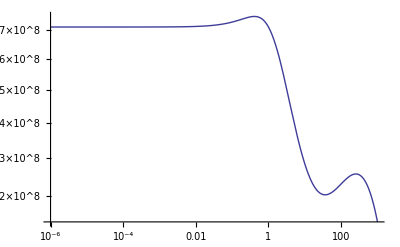

InterpolatingFunction::dmval: Input value {-13.8152} lies outside the range of data in the interpolating function. Extrapolation will be used.

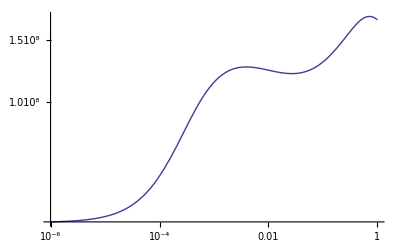

InterpolatingFunction::dmval: Input value {-0.0951244} lies outside the range of data in the interpolating function. Extrapolation will be used.

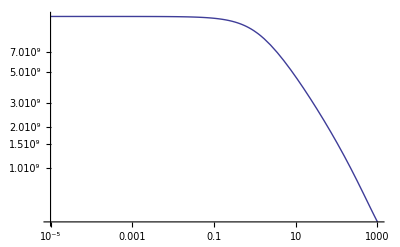

InterpolatingFunction::dmval: Input value {-6.90761} lies outside the range of data in the interpolating function. Extrapolation will be used.

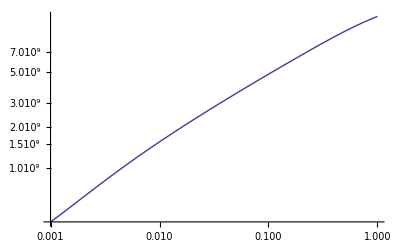

NIntegrate::nlim: x = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

InterpolatingFunction::dmval: Input value {1/3201} lies outside the range of data in the interpolating function. Extrapolation will be used.

2.72598×10^8

0.468618

{5.61648}

{5.61648}

```mathematica
(*********************************************)
Print[Style["Normalization factors. normalized to a early time of about a=10^-3",30,Bold,Orange]]
(*********************************************)
(*Manually set the criteria for the element in aokTabL etc that corresponds to normalization time.*)
(*nort=197-tranzL*)
Clear[k1,k2]
k1=PowerS[[nort1,1]]
k2=PowerS[[nort2,1]]
s12=NDSolve[{(x mH1[x])Gm1''[x]==-((1+6 δ2 λ1[x])mH1[x]+mH1[x]+x mH1'[x])Gm1'[x]-3δ2 (mH1'[x]λ1[x]+mH1[x]λ1'[x]+mH1[x]/x λ1[x](1+3δ2 λ1[x]))Gm1[x]+3δ2 (mH1[x]/x λ1[x](1+3δ2 λ1[x])+mH1[x]+x mH1'[x])Gd1[x]+3δ2 mH1[x]λ1[x]Gd1'[x]+3/2 mH1[x]/x Ωm0 Gm1[x]+3/2 mH1[x]/x(1-Ωm0)Gd1[x],x^2 Gd1''[x]== -(2+3 ce21 -3w1 -3 δ2/(w1+1)+x mH1'[x]/mH1[x]) x Gd1'[x]+(-3 ce21 x mH1'[x]/mH1[x]+3(δ2+w1)mH1'[x]/mH1[x] x-k1^2 ce21 (1/mH1[x])^2+3/2(1+w1)x^(-3(1+w1+δ2))+3(w1-ce21)(1-3 δ2/(1+w1))) Gd1[x]+3/2(1+w1)(Ωm0 Gm1[x]+(1-Ωm0)Gd1[x]),Gm1[1/3201]==N[GrowthL2[1/3201]],Gm1'[1/3201]==0,Gd1[1/3201]==1/3 N[GrowthL2[1/3201]],Gd1'[1/3201]==0},{Gm1,Gd1},{x,0.001,1}]
GrowthDE1[x_]=Gm1[x]/.s12
Clear[x]
s22=NDSolve[{(x mH2[x])Gm2''[x]==-((1+6 δ2 λ2[x])mH2[x]+mH2[x]+x mH2'[x])Gm2'[x]-3δ2 (mH2'[x]λ2[x]+mH2[x]λ2'[x]+mH2[x]/x λ2[x](1+3δ2 λ2[x]))Gm2[x]+3δ2 (mH2[x]/x λ2[x](1+3δ2 λ2[x])+mH2[x]+x mH2'[x])Gd2[x]+3δ2 mH2[x]λ2[x]Gd2'[x]+3/2 mH2[x]/x Ωm0 Gm2[x]+3/2 mH2[x]/x(1-Ωm0)Gd2[x],x^2 Gd2''[x]== -(2+3 ce21 -3w2 -3 δ2/(w2+1)+x mH2'[x]/mH2[x]) x Gd2'[x]+(-3 ce22 x mH2'[x]/mH2[x]+3(δ2+w2)mH2'[x]/mH2[x] x-k2^2 ce22 (1/mH2[x])^2+3/2(1+w2)x^(-3(1+w2+δ2))+3(w2-ce22)(1-3 δ2/(1+w2))) Gd2[x]+3/2(1+w2)(Ωm0 Gm2[x]+(1-Ωm0)Gd2[x]),Gm2[1/3201]==N[GrowthL2[1/3201]],Gm2'[1/3201]==0,Gd2[1/3201]==1/3 N[GrowthL2[1/3201]],Gd2'[1/3201]==0},{Gm2,Gd2},{x,0.001,1}]
GrowthDE2[x_]=Gm2[x]/.s22

LogLogPlot[Gd2[1/(1+z)]/.s22,{z,0.000001,1000}]
LogLogPlot[Gd2[a]/.s22,{a,0.000001,1}]
LogLogPlot[Gm1[1/(1+z)]/.s12,{z,0.00001,1000}]
LogLogPlot[Gm1[a]/.s12,{a,0.001,1},PlotRange->Full]

N[GrowthL2[1/3201]]
fracs=1/((Growths[1]/Growths[aokTabs[[norts]]])/(GrowthL[1]/GrowthL[aokTabL[[norts]]]))
frac1=1/(((Gm1[1]/.s12)/(Gm1[aokTabDE1[[nort1]]]/.s12))/(GrowthL[1]/GrowthL[aokTabL[[nort1]]]))
frac2=1/(((Gm2[1]/.s22)/(Gm2[aokTabDE2[[nort2]]]/.s22))/(GrowthL[1]/GrowthL[aokTabL[[nort2]]]))
```

```mathematica
{5.616482325309141}
```

```mathematica
Clear[x,k1,k2]
s12:=NDSolve[{(x mH1[x])Gm1''[x]==-((1+6 δ2 λ1[x])mH1[x]+mH1[x]+x mH1'[x])Gm1'[x]-3δ2 (mH1'[x]λ1[x]+mH1[x]λ1'[x]+mH1[x]/x λ1[x](1+3δ2 λ1[x]))Gm1[x]+3δ2 (mH1[x]/x λ1[x](1+3δ2 λ1[x])+mH1[x]+x mH1'[x])Gd1[x]+3δ2 mH1[x]λ1[x]Gd1'[x]+3/2 mH1[x]/x Ωm0 Gm1[x]+3/2 mH1[x]/x(1-Ωm0)Gd1[x],x^2 Gd1''[x]== -(2+3 ce21 -3w1 -3 δ2/(w1+1)+x mH1'[x]/mH1[x]) x Gd1'[x]+(-3 ce21 x mH1'[x]/mH1[x]+3(δ2+w1)mH1'[x]/mH1[x] x-PowerS[[n1+tranzDE1,1]]^2 ce21 (1/mH1[x])^2+3/2(1+w1)x^(-3(1+w1+δ2))+3(w1-ce21)(1-3 δ2/(1+w1))) Gd1[x]+3/2(1+w1)(Ωm0 Gm1[x]+(1-Ωm0)Gd1[x]),Gm1[1/3201]==N[GrowthL2[1/3201]],Gm1'[1/3201]==0,Gd1[1/3201]==1/3 N[GrowthL2[1/3201]],Gd1'[1/3201]==0},Gm1,{x,0.001,1}]
GrowthDE1[x_]:=s12
s22:=NDSolve[{(x mH2[x])Gm2''[x]==-((1+6 δ2 λ2[x])mH2[x]+mH2[x]+x mH2'[x])Gm2'[x]-3δ2 (mH2'[x]λ2[x]+mH2[x]λ2'[x]+mH2[x]/x λ2[x](1+3δ2 λ2[x]))Gm2[x]+3δ2 (mH2[x]/x λ2[x](1+3δ2 λ2[x])+mH2[x]+x mH2'[x])Gd2[x]+3δ2 mH2[x]λ2[x]Gd2'[x]+3/2 mH2[x]/x Ωm0 Gm2[x]+3/2 mH2[x]/x(1-Ωm0)Gd2[x],x^2 Gd2''[x]== -(2+3 ce21 -3w2 -3 δ2/(w2+1)+x mH2'[x]/mH2[x]) x Gd2'[x]+(-3 ce22 x mH2'[x]/mH2[x]+3(δ2+w2)mH2'[x]/mH2[x] x-PowerS[[n2+tranzDE2,1]]^2 ce22 (1/mH2[x])^2+3/2(1+w2)x^(-3(1+w2+δ2))+3(w2-ce22)(1-3 δ2/(1+w2))) Gd2[x]+3/2(1+w2)(Ωm0 Gm2[x]+(1-Ωm0)Gd2[x]),Gm2[1/3201]==N[GrowthL2[1/3201]],Gm2'[1/3201]==0,Gd2[1/3201]==1/3 N[GrowthL2[1/3201]],Gd2'[1/3201]==0},Gm2,{x,0.001,1}]
GrowthDE2[x_]:=s22
```

NIntegrate::nlim: x = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

InterpolatingFunction::dmval: Input value {1/3201} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

InterpolatingFunction::dmval: Input value {1/3201} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Table[GrowthDE1[aokTabDE1[[n1]]],{n1,1,leth-tranzDE1}]
Table[GrowthDE2[aokTabDE2[[n2]]],{n2,1,leth-tranzDE2}]
```

NIntegrate::nlim: x = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

InterpolatingFunction::dmval: Input value {1/3201} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

InterpolatingFunction::dmval: Input value {1/3201} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndode: Input is not an ordinary differential equation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1/3201} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndode: Input is not an ordinary differential equation.

General::stop: Further output of NDSolve :: ndode will be suppressed during this calculation.

{NDSolve[{«1»},Gm1,{x,0.001,1}],NDSolve[{«1»},Gm1,{x,0.001,1}],NDSolve[«1»],NDSolve[{«1»},Gm1,{x,0.001,1}],NDSolve[{71. x^2 √(0.0000809/x^4+0.27/x^3-(0.81111 (-1.×10^-6-0.9 x^2.7))/x^3) Gm1''[x]==«7»+(-71. x √(0.0000809/x^4+0.27/x^3-(0.81111 (-1.×10^-6-0.9 x^2.7))/x^3)-71. x √(0.0000809/x^4+0.27/x^3-(0.81111 (-1.×10^-6-0.9 x^(«9»)))/x^3) (1-(4.38×10^-6 x^2.7)/(0.27+8.1111×10^-7 (1-x^2.7)))-x ((35.5 x (-0.0003236/x^5-0.81/x^4+1.971/x^1.3+(2.43333 (-1.×10^-6-0.9 x^2.7))/x^4))/(√(0.0000809/x^4+0.27/x^3-(0.81111 (-1.×10^-6-0.9 x^2.7))/x^3))+71. √(0.0000809/x^4+0.27/x^3-(0.81111 (-1.×10^-6-0.9 x^2.7))/x^3))) Gm1'[x],«4»,Gd1'[1/3201]==0},Gm1,{x,0.001,1}],«99»,NDSolve[«1»],NDSolve[{«1»},Gm1,{x,0.001,1}],NDSolve[«1»],NDSolve[{«1»},Gm1,{x,0.001,1}],NDSolve[«1»]}

NIntegrate::nlim: x = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

InterpolatingFunction::dmval: Input value {1/3201} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

InterpolatingFunction::dmval: Input value {1/3201} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndode: Input is not an ordinary differential equation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1/3201} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndode: Input is not an ordinary differential equation.

General::stop: Further output of NDSolve :: ndode will be suppressed during this calculation.

{«1»}

NDSolve::ndode: Input is not an ordinary differential equation.

General::stop: Further output of NDSolve :: ndode will be suppressed during this calculation.

```mathematica
Qfactor1=Table[{PowerS[[n1+tranzDE1,1]],frac1 (Gm1[1/.s12]/Gm1[aokTabDE1[[n1]]])/(GrowthL[1]/GrowthL[aokTabL[[n1]]])},{n1,1,leth-tranzDE1}]
Qfactor1Ex=Table[{PowerS[[i]],frac1 (GrowthDE1[1]/GrowthDE1[aokTabDE1[[1]]])/(GrowthL[1]/GrowthL[aokTabL[[1]]])},{i,1,tranzDE1}]
Qfac1=Join[Qfactor1Ex,Qfactor1];
Qfactor1[[1]]
Qfac1[[1]][[1]]
Export["DEInteracting\\2012-02-21\\Qfac1.xls",Qfac1,"XLS"]
k1
Qfactor2=Table[{PowerS[[n2+tranzDE2,1]],frac2 (GrowthDE2[1]/GrowthDE2[aokTabDE2[[n2]]])/(GrowthL[1]/GrowthL[aokTabL[[n2]]])},{n2,1,leth-tranzDE2}]
Qfactor2Ex=Table[{PowerS[[i]],frac2 (GrowthDE2[1]/GrowthDE2[aokTabDE2[[1]]])/(GrowthL[1]/GrowthL[aokTabL[[1]]])},{i,1,tranzDE2}]
Export["DEInteracting\\2012-02-21\\Qfac2.xls",Qfac2,"XLS"]
k2
```

```mathematica
PowerSDE1=Table[{PowerS[[i,1]],(Qfac1[[i]][[2]])^2 PowerS[[i,2]]},{i,1,leth}];
PowerSDE2=Table[{PowerS[[i,1]],(Qfac2[[i]][[2]])^2 PowerS[[i,2]]},{i,1,leth}];
```

```mathematica
Export["DEInteracting\\2012-02-21\\PowerSDE1.xls",PowerSDE1,"XLS"]
Export["DEInteracting\\2012-02-21\\PowerSDE2.xls",PowerSDE2,"XLS"]
```

```mathematica
ListLogLogPlot[{PowerS,PowerSDE1,PowerSDE2},Joined->True,AxesLabel->{k,P},PlotRange->Automatic,PlotStyle->{Red,Black,Blue},PlotLegend->{"LCDM","w1","w2"},LegendPosition->{1.1,-0.4}]
```

```mathematica
ListLogLogPlot[{Qfac1,Qfac2},Joined->True, AxesLabel-> {k,Q},PlotRange->Full,PlotStyle->{Black,Blue},PlotLegend->{"w1","w2"},LegendPosition->{1.1,-0.4}]
```